```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/johannesk/kette_repo/limit_cycles/src_mathematica/good_fits

```mathematica
logspace[increments_,start_?Positive,end_?Positive]:=Exp@Range[Log@start,Log@end,Log[end/start]/increments];

LECsNUCL=Import["../LECs_nucl_Joki.dat","Table"][[2;;]];

activeLEC=LECsNUCL[[All,{1,2,3,4,5}]];
hbar=197.327053;
Mm=938.92;
m1=2 Mm;m2= Mm;
μ=m1 m2/(m1+m2);
mh2=(2 Mm)/(hbar)^2;
Print[1/mh2]
```

20.7355

```mathematica
I1[lam_,b1_,b2_] :=3Pi^(9/2)/(4(b1^3+b2^3+3b1^2 b2+3b2^2 b1+2 b1^2 lam+2 b2^2 lam+4 b1 b2 lam)^(3/2));
I2[lam_,b1_,b2_] := Pi^(9/2)/(2(b1^3+b2^3+3b1 b2^2+3b1^2 b2+(3/4)b1 lam^2+(3/4)b2 lam^2+4 b1^2 lam+4 b2^2 lam+2b1 b2 lam^2)^(3/2));
I3[b1_,b2_] :=9 b1 b2 Pi^(9/2)/(4(b1+b2)^(11/2));
```

```mathematica
ham[lam_,b1_,b2_,c0_,d1_]:=c0 I1[0.25 lam^2,b1,b2]+d1 I2[0.25 lam^2,b1,b2]+(1/mh2) I3[b1,b2];

norm[b1_,b2_]:=Module[{},Pi^(9/2)/(8(b1+b2)^(9/2))
]  ;
```

dimD:  bare basis dimension
widths: educated guess for the Gaussian width parameters each of which defines a bare basis function  e^(-β∑(r̄)^2)
lamd: cutoff/regularization parameter of the interaction
evlowthreshold: empirically determined threshold which sets the lower bound for the norm eigenvalues that are allowed in the
                                   stable, reduced basis

{-18.3879,-14.3828,-14.1076,-13.7012,-11.3362,-9.20298,-8.87835,-6.63964,-6.5695,-5.47975,-1.68994,-0.106127}

{-20830.,-4585.13+0. ⅈ,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,-1499.23-687.731 ⅈ,-1295.96+0. ⅈ,-775.957+0. ⅈ,ComplexInfinity,-32.0434+0. ⅈ,-19.9479+0. ⅈ,-19.5425,ComplexInfinity,-7387.74+0. ⅈ,-843.557+0. ⅈ,-18.9257+0. ⅈ,8.7666,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.78192+0. ⅈ,ComplexInfinity,ComplexInfinity}

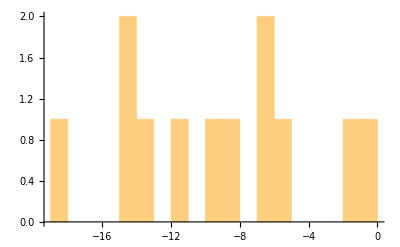

```mathematica
λ=10.0;
C0=Flatten[Select[activeLEC,#[[1]]==λ&]][[2]];
D1=0.25 Flatten[Select[activeLEC,#[[1]]==λ&]][[3]];

evlowthreshold=10^-10;
nbrW=25;

sigmi=3.0;

gsEresults={};
gsEresultsB={};
SetSharedVariable[gsEresults,gsEresultsB];

ParallelDo[
maxWi=0.1+nn 0.23;
le=0;
While[le==0,
dimD=22;
widths =Select[RandomVariate[NormalDistribution[maxWi,sigmi],dimD],#>0&];
dimD=Length[widths];
If[dimD>20,le=1];
];
hamm=Table[ham[λ,widths[[i]],widths[[j]],C0,D1],{i,dimD},{j,dimD}];
normm=Table[norm[widths[[i]],widths[[j]]],{i,dimD},{j,dimD}];

normDiag=DiagonalMatrix[1./Sqrt[Diagonal[normm]]];
HamN=(Transpose[normDiag].hamm).normDiag;
NormN=(Transpose[normDiag].normm).normDiag;

esn=Eigensystem[NormN];
evBare=Sort[Eigenvalues[{hamm,normm}],Re[#1]<Re[#2]&];
AppendTo[gsEresultsB,evBare[[1]]];

{μ,transf}=Transpose[Select[Sort[Transpose[esn],#1[[1]]<#2[[1]]&],#[[1]]>evlowthreshold&]];
(*Print[Length[μ]];*)
trafma=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);
traham=(Transpose[trafma].HamN).trafma;
esh=Eigensystem[traham];
{ϵ,transfe}=Transpose[Sort[Transpose[esh],#1[[1]]<#2[[1]]&]];
gsh=transfe[[1,All]];
(*Print["E_0^(bare) = ",Sort[evBare][[1]]];*)
If[Select[ϵ,#<0&]≠{},
AppendTo[gsEresults,ϵ[[1]]]
(*Print["Dim - Dim_reduced = ",dimD," - ",Length[μ],"     0H0 = ",gsh.traham.gsh," =^! ",ϵ[[1]],"   E_0^(bare) = ",Sort[evBare][[;;4]]]*)
];
,{nn,Range[1,nbrW]}];

Sort[gsEresults,#1<#2&]
Sort[gsEresultsB,Re[#1]<Re[#2]&]
Histogram[gsEresults,{1}]
```